## 1 Create a cloud expression

```mathematica
ce=CreateCloudExpression[Range[5]]
```

CloudExpression[…]

```mathematica
Get[ce]
```

{1,2,3,4,5}

```mathematica
AppendTo[ce,77]
```

CloudExpression[…]

```mathematica
Get[ce]
```

{1,2,3,4,5,77}

```mathematica
ce[[3]]=33
```

33

```mathematica
Get[ce]
```

{1,2,33,4,5,77}

```mathematica
ce[[2]]=.
```

```mathematica
Get[ce]
```

{1,33,4,5,77}

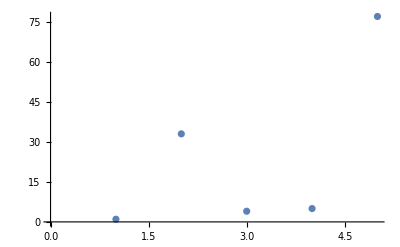

```mathematica
ListPlot[Get[ce]]
```

```mathematica
ce=CreateCloudExpression[Range[5],Permissions->"Public"]
```

CloudExpression[…]

```mathematica
ce=CreateCloudExpression[Range[5]]
```

CloudExpression[…]

```mathematica
Options[ce]
```

{Permissions→{Owner→{Read,Write,Execute}},PartProtection→Automatic}

```mathematica
SetPermissions[ce,"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

```mathematica
Options[ce]
```

{Permissions→{All→{Read},Owner→{Read,Write,Execute}},PartProtection→Automatic}